# Υπολογιστικά Μαθηματικά 2 2^ο σετ ασκήσεων

Τιτόνης Τρύφων

ΑΕΜ 4307

Αριστοτέλειο Πανεπιστήμιο Θεσσαλονίκης
Τμήμα Φυσικής

Άσκηση 7.4.2-2

Να κατασκευαστεί μια ρουτίνα που να δίνει τυχαίους αριθμούς, ομοιόμορφα κατανεμημένους στο διάστημα [0,1], χρησιμοποιώντας την αναδρομική σχέση

x_(n+1)=[a x_n+b]mod M

Μια καλή εκλογή των a, b, M για υπολογιστές 32-bit είναι a=1812433253, M=2^31-1 και b=περιττός.

Λύση

```mathematica
ClearAll["Global`*"]
randomLinearCongruential[number_,seed_,multiplier_,offset_,modulo_]:=Module[
{x,i,n,list},
(* ορισμός της αρχικής τιμής *)
x[0]=seed;
(* ορισμος της αναδρομικής σχέσης - η χρήση της ανάθεσης είναι απαραίτητη αν θέλουμε να κατασκευάζουμε μεγάλες λίστες αριθμων, έτσι ώστε να μην καθυστερεί το πρόγραμμα *)
x[n_]:=x[n]=Mod[multiplier x[n-1]+offset,modulo];
(* παραγωγή των πρώτων Ν αριθμών τυχαίων αριθμών *)
list=Table[x[i]/modulo,{i,1,number}]//N
]
```

Για παράδειγμα, οι 10 πρώτοι αριθμοί της ακολουθίας με αρχή τo 1, θα είναι οι παρακάτω:

```mathematica
randomLinearCongruential[10,1,1812433253,11,2^31-1]//TableForm
```

0.84398
0.0371973
0.0514313
0.673658
0.149316
0.47275
0.490906
0.831312
0.360002
0.297426

Ελέγχουμε αν όντως είναι σωστή η κατανομή των τυχαίων αριθμών που παίρνουμε:

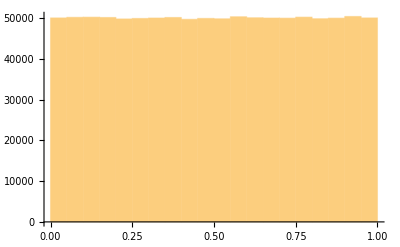

```mathematica
Histogram[randomLinearCongruential[1000000,1,1812433253,11,2^31-1]]
```

Όπως περιμέναμε η κατανομή είναι ομοιόμορφη.

Άσκηση 7.4.2-4

Με τη βοήθεια της ρουτίνας της άσκησης 7.4.2-2, δημιουργήστε Ν τυχαία ζεύγη καρτεσιανών συντενταγμένων (x,y) που να παριστάνουν τυχαία σημεία ενός τετραγώνου πλευράς δ, και μετρήστε αυτά που βρίσκονται μέσα στον εγγεγραμένο κύκλο (διαμέτρου δ). Διαπιστώστε ότι για Ν αρκετά μεγάλο, ο λόγος των σημείων που βρίσκονται στον κύκλο δια του Ν είναι ένα αριθμός πολύ κοντά στο π/4.

Λύση

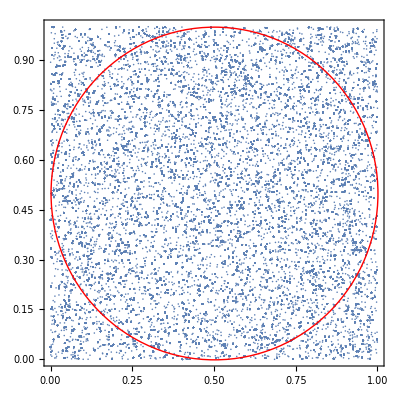

Με χρήση 100000 σημείων το π προσεγγίζεται στην τιμή: 3.13772

```mathematica
ClearAll[a,b,M,Num,seeds,pts,inCircle];
(* Ορισμός των παραμέτρων της τυχαίας κατανομής. *)a=1812433253b=11M=2^31-1;
(* Ορισμός του αριθμού των σημείων. *)Num=100000;
(* Ορισμός των αρχικών seed με βάση την τυχαία κατανομή. *)seeds=randomLinearCongruential[2,1,a,b,M];
(* Εύρεση των σημείων. *)
pts=Transpose@{randomLinearCongruential[Num,seeds[[1]],a,b,M],
randomLinearCongruential[Num,seeds[[2]],a,b,M]};
(* Σχεδιασμός των σημείων. *)
ListPlot[pts,
Frame->True,
AspectRatio->1/1,
PlotRange->{{0,1},{0,1}},
Epilog->{Red,Circle[{0.5,0.5},0.5]}
]
(* Μέτρηση του αριθμού των σημείων μέσα στον κύκλο. *)
inCircle=Count[pts,x_/;√((x[[1]]-0.5)^2+(x[[2]]-0.5)^2)≤0.5];
(* Υπολογισμός του π. *)
StringForm["Με χρήση `` σημείων το π προσεγγίζεται στην τιμή: ``",Num,FullForm@N[4 inCircle/Num]]
```

Εκτελούμε τη μέτρηση, αλλάζοντας κάθε φορά το seed και τον αριθμό των σημείων, για να δούμε αν υπάρχει σύγκλιση στην τιμή του π όσο αυξάνονται τα σημεία, και επίσης αν επηρρεάζεται η μέτρηση από την αρχική τιμής της γεννήτριας.

```mathematica
ClearAll[a,b,M,count,results,pts,Num,seeds,inCircle]
a=1812433253;b=11;M=2^31-1;
count=7;
results=ConstantArray[0,{count}];
For[i=1,i≤count,i++,
Num=10^i;
seeds=randomLinearCongruential[2,i,a,b,M];
pts=Transpose@{
randomLinearCongruential[Num,seeds[[1]],a,b,M],
randomLinearCongruential[Num,seeds[[2]],a,b,M]
};
inCircle=Count[pts,x_/;√((x[[1]]-0.5)^2+(x[[2]]-0.5)^2)≤0.5];
results[[i]]={Num,N[4 inCircle/Num]};
];
TableForm[Map[FullForm,results,{2}],
TableAlignments->Center,
TableHeadings->{Range[count],{"αριθμός σημείων","πρόβλεψη π"}}
]
```

| αριθμός σημείων | πρόβλεψη π
1 | 10 | 2.8
2 | 100 | 3.2
3 | 1000 | 3.136
4 | 10000 | 3.1388
5 | 100000 | 3.11752
6 | 1000000 | 3.16846
7 | 10000000 | 3.04391

Όπως φαίνεται από τα παραπάνω, πλησιάζουμε προς την πραγματική τιμή του π όσο αυξάνουμε τα σημεία, όμως ταυτόχρονα, η επιλογή των παραμέτρων φαίνεται ότι δεν είναι η καλύτερη, μιας και επηρεάζει αρνητική την σύγκλιση.

Άσκηση 7.4.2-5

Να γίνει το ιστόγραμμα ενός μεγάλου αριθμού τιμών που δημιουργούνται από τη ρουτίνα RNDGAUSS1. Να διαπιστώσετε ότι η κατανομή τους προσεγγίζει την κανονική κατανομή με μ=0 και σ^2=1. Να γίνει η σύγγριση των αποτελεσμάτων αν αντί 12 ομοιόμορφα κατανεμμένων Τ.Α. χρησιμοποιηθούν 6 ή 12. Στις περιπτώσεις αυτές οι μέσες τιμές και οι διασπορές είναι 3, 12 και 1/2, 2, αντίστοιχα.

Λύση

Ορίζουμε την συνάρτηση rndgauss1:

```mathematica
ClearAll[rndgauss1];
rndgauss1[n_]:=Module[
{rnd=0,i,a=1812433253,b=11,M=2^31-1,seed},
seed=Apply[Plus,DateList[Now]];
Total@randomLinearCongruential[n,seed,a,b,M]-n/2
]
```

Δημιουργούμε έναν μεγάλο αριθμό αριθμών με χρήση της παραπάνω συνάρτησης, σχεδιάζουμε το 
ιστόγραμμά τους, και υπολογίζουμε την μέση τιμή και την απόκλισή τους, και για τις τρεις περιπτώσεις.

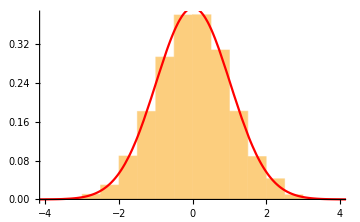
Αθροίσματα 12 τυχαίων αριθμών
-Graphics-
Η μέση τιμή των αποτελεσμάτων είναι: 0.0132254
Η διασπορά των αποτελεσμάτων είναι: 1.00978

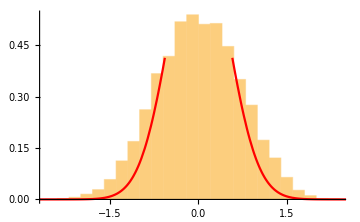
Αθροίσματα 6 τυχαίων αριθμών
-Graphics-
Η μέση τιμή των αποτελεσμάτων είναι: 0.00220272
Η διασπορά των αποτελεσμάτων είναι: 0.499606

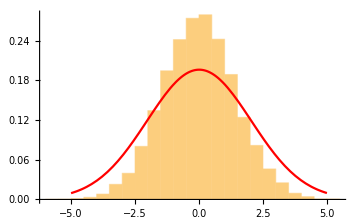
Αθροίσματα 24 τυχαίων αριθμών
-Graphics-
Η μέση τιμή των αποτελεσμάτων είναι: 0.00696771
Η διασπορά των αποτελεσμάτων είναι: 2.0352

```mathematica
ClearAll[results,n,mu,sigma2]
Do[
n=25000;
results=Table[rndgauss1[k],{n}];
mu=Total[results]/n;
sigma2=(Total@Map[(#-Mean[results])^2&,results])/(Length[results]-1);
Print@Column[{
Style[StringForm["Αθροίσματα `` τυχαίων αριθμών",k],{Bold,Larger}],
Histogram[results,Automatic,"PDF",ImageSize->Medium,
Epilog->First@Plot[PDF[NormalDistribution[mu,sigma2],x],{x,-5,5},PlotStyle->Red]],
StringForm["Η μέση τιμή των αποτελεσμάτων είναι: ``",mu],
StringForm["Η διασπορά των αποτελεσμάτων είναι: ``",sigma2],
""
},Alignment->Center]
,{k,{12,6,24}}]
```

Παρατηρούμε ότι στις περιπτώσεις για 6 και 24 σημεία η αντίσοιτχη κανονικη κατανομή (κόκκινη γραμμή στα διαγράμματα) δεν ταιριάζει πολύ καλά με το ιστόγραμμα. Αντιθέτως, στην πρώτη περίπτωση έχουμε εξαιρετική ταύτιση.